```mathematica
V=30;
th=50*Pi/180;
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)
x[0]=0;
x'[0]=V Cos[th];
y[0]=2
y'[0]=V Sin[th]
θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
v=30;
c=1
m=10;
vt=300;
x[t]=x[0]+V Cos[Th*t];
y[t]=y[0]+V Sin[Th*t]-.5*g*t^2;
ode1={x''[t]==(-g x'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]
y''[t]==-g(1+(y'[t]/vt^2))Sqrt[x'[t]^2+y'[t]^2]};
sol=NDSolve[ode1,{x,y},{t,0,200}];
```

2

30 Cos[(2 π)/9]

1

NDSolve::underdet: There are more dependent variables, {30\ Cos[t\ Th], 2 - 4.9\ t^2 + 30\ Sin[t\ Th]}, than equations, so the system is underdetermined.

```mathematica
myplot1 = ParametricPlot[{x[t],y[t]},{t,0,200}]
```

-Graphics-

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

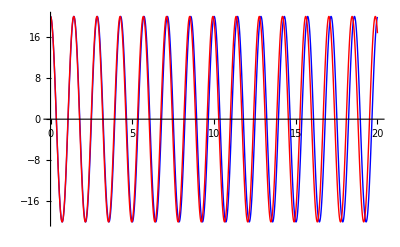

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

```mathematica
c=.5;
rho=1.29;
Vter=√(2m*g/(C*rho*A));
Manipulate[
Vter=135; m=6; A=9.9*10^(-3);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

14. √(1/(A C rho))